## Problem Set 1

## Horia Magureanu (DPhil Student)

Question 1

Let us first define a function that computes the arithmetic-geometric mean of two numbers a, b to an accuracy acc.

```mathematica
Clear[a,b,M,x,y];
M[x_,y_,acc_]:=
Module[{a=x, b=y,c=acc},
While[Abs[a-b]>10^(-(c+1)),
		a=N[1/2(a+b),c];
		b=N[((2a-b)b)^(1/2),c];]; (*This is needed as b changes at the previous iteration*)
	a];
```

Let us now check the function:

```mathematica
N[M[24,6,100],40]
```

13.45817148172561542076681315697439924305

The Integral given in the problem:

```mathematica
ω=N[2 Integrate[1/((1-x^4)^(1/2)),{x,0,1}],120];
```

We can now check Gauss’s claim:

```mathematica
N[N[M[1,√2 ,120],120]-N[π/ω,120],100]
```

0.

Question 2

Define the functions F(x) and I(a) as described in the problem:

```mathematica
Clear[F,x,I0,a];
F[x_]:=5^(5I x)Gamma[1-5I x]/Gamma[1-I x]^5;
I0[a_]:=Integrate[(x Re[F[x]]Cos[a x])/(1-Exp[-2π x]),{x,-∞,∞}];
```

We use the function Series on x F(x) first. This is relevant since for large x, the prefactor of the cosine is essentially x F(x):

```mathematica
Normal[Series[x F[x],{x,∞,1}]]
```

-(√5)/(4 π^2 x)

Let us now plot the integrand, to see the behaviour of the function that multiplies the cosine:

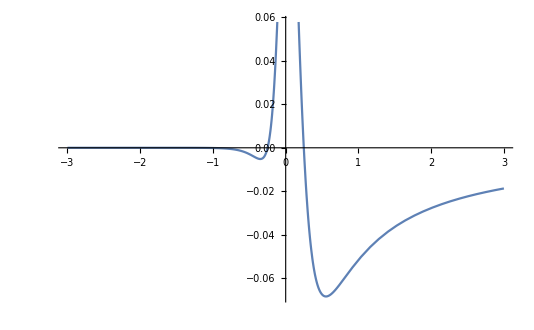

```mathematica
Plot[(x Re[F[x]])/(1-Exp[-2π x]),{x,-3,3}]
```

Note that for large negative values of x, the exponential term in the denominator dominates, so the function diverges very fast. Thus, the only relevant contribution for negative x comes from the area around the origin.
We can also check to see how good of an approximation the leading term of x F(x) is for positive x:

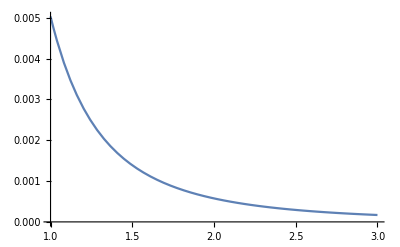

```mathematica
Plot[(x Re[F[x]])/(1-Exp[-2π x])+(√5)/(4 π^2 x),{x,1,3}]
```

We can now break the integral into two parts. For x>1 we can use the previous approximation, while for x<1 we only take the leading term of the cosine (i.e. 1).
The J integral is essentially a ‘CosIntegral’, which can be approximated for real a>0 (this can be of course done for negative a as well, the difference being an iπ term coming from the logarithm):

```mathematica
Series[(-√5)/(4 π^2)Integrate[Cos[a x]/x,{x,1,∞}, Assumptions->a>0],{a,0,2}]
```

(√5 EulerGamma+√5 Log[a])/(4 π^2)-(√5 a^2)/(16 π^2)+O[a]^3

We thus obtain the leading term in a, so we are only looking for the constant term C. As a result, we set a=0 in the integral (-∞,1) to find that C is approximately given by:

```mathematica
N[NIntegrate[(x Re[F[x]])/(1-Exp[-2π x]),{x,-∞,1},WorkingPrecision->40,AccuracyGoal->20]+(√5 EulerGamma)/(4 π^2),120]
```

0.02956295811166244149155045454704301504825

We can improve our estimate by increasing the WorkingPrecision and AccuracyGoal:

```mathematica
N[NIntegrate[(x Re[F[x]])/(1-Exp[-2π x]),{x,-∞,1},WorkingPrecision->200,AccuracyGoal->120]+(√5 EulerGamma)/(4 π^2),120]
```

0.0295629581116624414915504545470430181260675997462448655061575778683270825967307435646725002726228527715110346193756964121

Question 3

We start by defining the two functions and plotting them together:

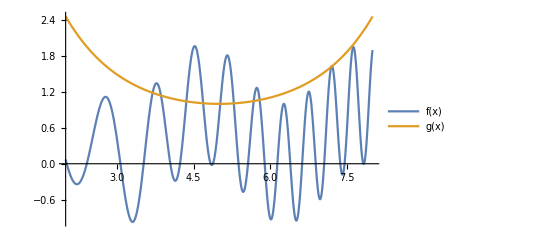

```mathematica
Clear[f,g,x]
f[x_]:=Sin[x^2]+Sin[x]^2;
g[x_]:=Exp[(5-x)^2/10];
Plot[{f[x],g[x]},{x,2,8}, PlotLegends->"Expressions"]
```

The number of roots of f(x)=g(x) can be found using the function CountRoots. Let us note that f(x)≤2 for any value of x, while g(x)<2 only for a region around its minimum. From the plot, we can safely limit this region to [2,8]. Hence, the number of roots is:

```mathematica
CountRoots[f[x]-g[x],{x,2,8}]
```

10

We can now try to find the (approximate) values of these roots using the FindRoot function. This function requires a starting value; initially this will be set to 3 (since the first root is higher than this, which can be observed from the plot), after which we will  increase this in constant steps. If the root is more than 0.1 away from the initial value, we will discard it, since we will cover the interval in steps of this size anyways. We choose to proceed in this way since the FindRoot function does not always give the closest root to the initial value, unless these two are very close to each other.

```mathematica
Clear[x0,i,a]
x0=3; i=1;
While[x0<8,
	Clear[a];
	a=FindRoot[f[x]==g[x],{x,x0},WorkingPrecision->140,AccuracyGoal->60][[1]][[2]];
	If[Abs[a-x0]<0.005, 
		{Print[i,") ",a]; i++}
		];
	x0=x0+0.01;
	If[i==11,Break[]];
	]
```

1) 3.7003907229884175923476756008533860420328495400814229565492229824124565292652679571775746725234651621858419709406958894775807468470427413845

2) 3.8642125274802395000212520812277297566449101437052520466085211214224540731617790299368264766682342640913594066373918835623095101102757059636

3) 4.3601673273388477617900458873932246221524056954930980171088339386736017462095530986326146216661784243952581669497237558886572698234079745822

4) 4.688369967633294590605283895415308935686344611769950579203337033335442304802427589439792776972370393900517284238576908611552182113156577958

5) 5.022557762484828024817570485879263381415046045946032223347161600974325904556413367067431499221122891961279182760012424357084823102506000894

6) 5.2881574882517039658440841056697027569620390374170963710488798259294940393607773836843534057704568437756072065043217886076566449021017082404

7) 5.6764608788280544456317407144313215823167915358752639921540542694128012166508116891940468629077634798770172003701289608991446236436794408881

8) 5.7926539493703624867940203355159091761727881576065187752624459835791908207068775611914170263191590288108921068473400174379979781070542721292

9) 7.1924940248612364671296562852220863573914918245916037505635515770358255897369105988821319733466697788435959281930899689337790372996572430823

10) 7.2094017568900782623300025753575019255243993938295947981272673135727380750131067053593796018825796945460582707483757993074649095602301814709

Question 4

We start by generating two symmetric 8x8 matrices with entries in (-1,1). Also define the one parameter family of matrices M(t):

```mathematica
Clear[A,B,t,M,EigenVs];

rmat:=RandomReal[{−1,1},{8,8}];
A=rmat; A=(A+Transpose[A])/2;
B=rmat; B=(B+Transpose[B])/2;
M[t_]:=t A+(1-t)B;
```

Let us now plot the eigenvalues of M(t):

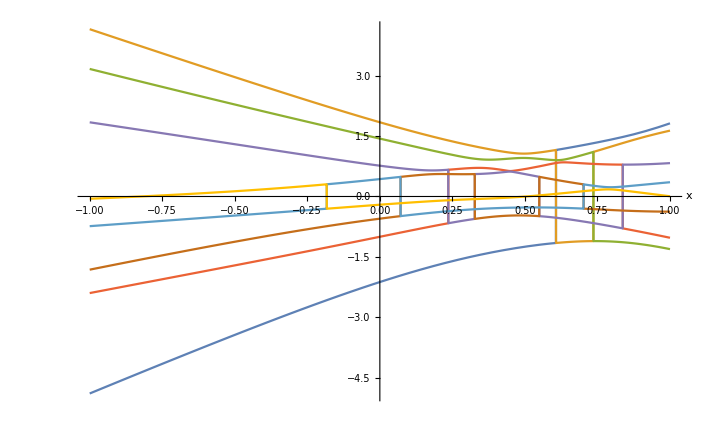

```mathematica
EigenVs:=Eigenvalues[M[x]];
Plot[EigenVs,{x,-1,1},AxesLabel->Automatic]
```

The plot seems rather messy, so let us Sort the eigenvalues before plotting them:

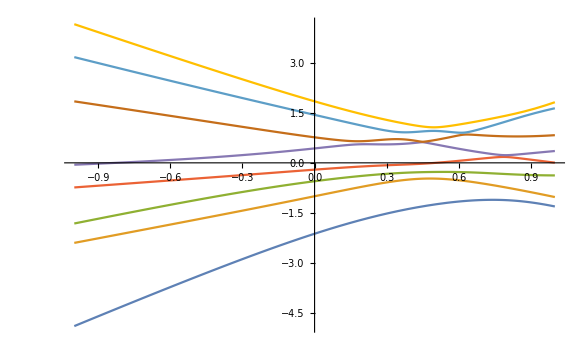

```mathematica
EigenVs:=Sort[Eigenvalues[M[x]]];
Plot[EigenVs,{x,-1,1}]
```

It does indeed seem like some of the curves do cross each other. Zooming in we do see that they do not actually cross. We can also plot the curves separately and see that the slope changes drastically at some points.

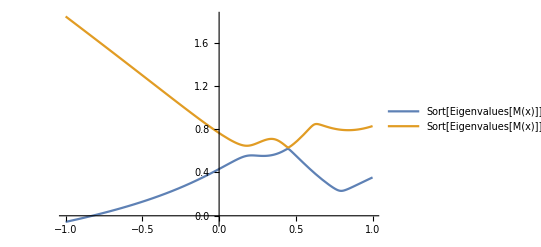

```mathematica
Plot[{Sort[Eigenvalues[M[x]]][[5]],Sort[Eigenvalues[M[x]]][[6]]},{x,-1,1},PlotLegends->"Expressions"]
```

Alternatively, we can use Solve to find the possible intersections, but in this case there are none:

```mathematica
Solve[Sort[Eigenvalues[M[x]]][[5]]==Sort[Eigenvalues[M[x]]][[6]],x]
```

{{}}

Without the sorting, two curves would look like:

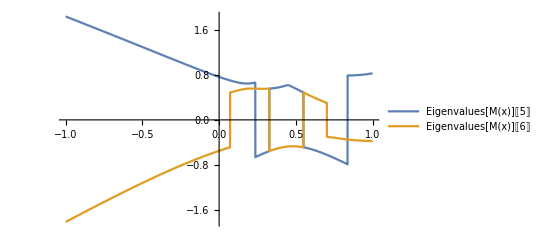

```mathematica
Plot[{Eigenvalues[M[x]][[5]],Eigenvalues[M[x]][[6]]},{x,-1,1},PlotLegends->"Expressions"]
```

Possible intersections would be given by:

```mathematica
Solve[Eigenvalues[M[x]][[5]]==Eigenvalues[M[x]][[6]],x]
```

{{}}

This again leads to no solutions, despite the fact that the curves ‘seem’ to intersect. This is because the functions have discontinuities at the points where their values drastically change, such as:

```mathematica
Eigenvalues[M[0.23598]][[5]]
Eigenvalues[M[0.23599]][[5]]
```

0.663831

-0.663836

Question 5

We start by creating a function that solves the equation for integers and returns the unique ways of decomposing a given integer in a sum of two cubes:

```mathematica
Clear[n,x,y,a,l,Ram];
Ram[a_]:=Solve[a==x^3+y^3 && x≥y && y>0,{x,y}, Integers]; (*This is not great, but can probably check up to (n/2)^(1/3)*)
```

```mathematica
Ram[4104]
```

{{x→15,y→9},{x→16,y→2}}

We are now interested in finding the smallest integer that can be written as two different sums of cubes. A (probably inefficient) way of doing this is to apply the Ram[] function for every integer from 2 as:

```mathematica
n=2;
While[True,
	If[Length[Ram[n]]>1, (*Could put ==2, but let us just look for >1 instead*)
			Print[n]; Break[],
			n++]]
```

1729

The next integer that satisfies this property can be computed in a similar way (and we see that it is 4104):

```mathematica
n++;
While[True,
	If[Length[Ram[n]]>1,
			Print[n]; Break[],
			n++]]
```

4104